```mathematica
SetDirectory["/Users/mobileryan/Triplet-ESR"]
```

/Users/mobileryan/Triplet-ESR

```mathematica
Directory[]
```

C:\Users\goluc\Documents

```mathematica
SetDirectory["C:\\Users\\goluc\\Desktop\\nonLinearFit"]
```

C:\Users\goluc\Desktop\nonLinearFit

```mathematica
preData=Import["./test.dat","CSV" ];
{dimT, dump}=Dimensions[preData[[2;;-1]]]
BData=Drop[Drop[preData[[1]],1],-1];
dimB=Length[BData]
DataB[B_]:=Table[{preData[[i,1]],preData[[i,B+1]]},{i,2,dimT}]
DataT[t_]:=Table[{preData[[1,i]],preData[[t+1,i+1]]},{i,1,dimB}]
```

{1002,352}

350

```mathematica
tempData=preData[[2;;-1, 2;;-1]];
ArrayPlot[tempData,ColorFunction->"Rainbow",AspectRatio->1]
{Max[tempData], Min[tempData]}
```

-Graphics-

{Max[41.34,],Min[-34.17,]}

```mathematica
Manipulate[
Module[{dataT},
dataT=DataT[startT];
ListPlot[dataT,Joined->True, AspectRatio->1/10,PlotRange->All, ImageSize->Full, PlotLabel->ToString[startT]<>", Time = "<>ToString[preData[[startT+1,1]]]<>", Max = "<> ToString[Max[dataT[[1;;-1,2]]]]<>", Min = "<>ToString[ Min[dataT[[1;;-1,2]]]]] 
],
{{startT,207},1,dimT,1}]
```

```mathematica
Manipulate[
Module[{dataB},
dataB=DataB[startB];
ListPlot[dataB,Joined->True, AspectRatio->1/10,PlotRange->All, ImageSize->Full, PlotLabel->ToString[startB]<>", B-field = "<>ToString[preData[[1,startB]]]<>", Max = "<> ToString[Max[dataB[[1;;-1,2]]]]<>", Min = "<>ToString[ Min[dataB[[1;;-1,2]]]]]
] ,
{{startB,105},1,dimB,1}]
```

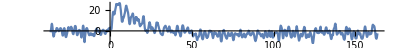

{B-Field,3.217,2.8,mean,-0.579605,sd,2.86842}

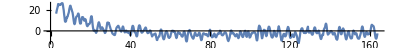

```mathematica
startB=105;
dataB=DataB[startB];
fitStartT=197;
ListPlot[dataB, Joined->True, AspectRatio->1/10,PlotRange->All, ImageSize->Full] 
{"B-Field",BData[[startB]],dataB[[fitStartT,1]],"mean",noiseLevel=Mean[dataB[[1;;fitStartT-20,2]]], "sd",sd=StandardDeviation[dataB[[1;;fitStartT-20,2]]]}
g1=ListPlot[dataB[[fitStartT;;-1]], Joined->True, AspectRatio->1/10,PlotRange->All, ImageSize->Full]
```

```mathematica
Func[t_,a_,Ta_]:=a Exp[-t/Ta]
f[t_,par_]:=Func[t,par[[1]],par[[2]]]+Func[t,par[[3]],par[[4]]]
F[t_,par_]:={ⅇ^(-t/par[[2]]),(par[[1]] ⅇ^(-t/par[[2]]) t)/par[[2]]^2,ⅇ^(-t/par[[4]]),(par[[3]] ⅇ^(-t/par[[4]]) t)/par[[4]]^2}
F2[t_,par_]:={ⅇ^(-t/par[[2]]),(par[[1]] ⅇ^(-t/par[[2]]) t)/par[[2]]^2}
```

{ | Estimate | Standard Error | t-Statistic | P-Value
a | 38.9404 | 2.484 | 15.6765 | 2.2895×10^-48
Ta | 20.2724 | 1.9242 | 10.5355 | 2.32079×10^-24
b | -9.32232 | 2.9201 | -3.19247 | 0.00146706
Tb | 98.6631 | 25.7159 | 3.83665 | 0.000134778, | DF | SS | MS
Model | 4 | 26345.8 | 6586.46
Error | 782 | 8446.37 | 10.801
Uncorrected Total | 786 | 34792.2 | 
Corrected Total | 785 | 34775.5 | , | Estimate | Standard Error | Confidence Interval
a | 38.9404 | 2.484 | {34.0643,43.8165}
Ta | 20.2724 | 1.9242 | {16.4952,24.0496}
b | -9.32232 | 2.9201 | {-15.0545,-3.59016}
Tb | 98.6631 | 25.7159 | {48.1826,149.144}}

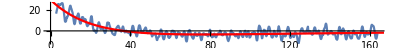

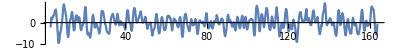

{mean,0.0615837,sd,3.31479,1.15562}

```mathematica
nlm=NonlinearModelFit[dataB[[fitStartT;;-20]],{f[t,{a,Ta,b,Tb}], 100>a>0, b<0, 0<Ta <Tb}, {a, Ta, b, Tb}, t];
nlm[{"ParameterTable","ANOVATable","ParameterConfidenceIntervalTable"}]
Show[
g1,
Plot[nlm[t],{t,0,200}, PlotRange->All, PlotStyle->Red]
]
diff=Table[{dataB[[i,1]],dataB[[i,2]]-nlm[dataB[[i,1]]]},{i,200,Length[dataB]}];
ListPlot[diff, Joined->True, AspectRatio->1/10,PlotRange->All, ImageSize->Full]
{"mean",Mean[diff[[1;;-1,2]]], "sd",fitSigma=StandardDeviation[diff[[1;;-1,2]]], fitSigma/sd}
```

{ | Estimate | Standard Error | t-Statistic | P-Value
a | 43.2005 | 0.907993 | 47.5781 | 3.98102×10^-236
Ta | 18.0898 | 0.468966 | 38.5738 | 3.69199×10^-185, | DF | SS | MS
Model | 2 | 64018.5 | 32009.3
Error | 805 | 8658.36 | 10.7557
Uncorrected Total | 807 | 72676.9 | 
Corrected Total | 806 | 64550.3 | , | Estimate | Standard Error | Confidence Interval
a | 43.2005 | 0.907993 | {41.4182,44.9828}
Ta | 18.0898 | 0.468966 | {17.1693,19.0104}}

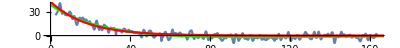

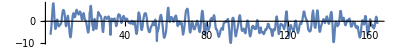

{mean,-1.00226,sd,3.05819,1.04221}

```mathematica
nlm2=NonlinearModelFit[dataB[[fitStartT;;-1]],{Func[t,a,Ta], 100>a>0, 0<Ta}, {a, Ta}, t];
nlm2[{"ParameterTable","ANOVATable","ParameterConfidenceIntervalTable"}]
Show[
g1,
Plot[nlm[t],{t,0,200}, PlotRange->All, PlotStyle->Green],
Plot[nlm2[t],{t,0,200}, PlotRange->All, PlotStyle->Red]
]
diff2=Table[{dataB[[i,1]],dataB[[i,2]]-nlm2[dataB[[i,1]]]},{i,200,Length[dataB]}];
ListPlot[diff2, Joined->True, AspectRatio->1/10,PlotRange->All, ImageSize->Full]
{"mean",Mean[diff2[[1;;-1,2]]], "sd",fitSigma2=StandardDeviation[diff2[[1;;-1,2]]], fitSigma2/sd}
```

## Manual Method

```mathematica
newPar[par_,dataB_]:=Module[
{fa,Fa, Y,X, par1,CoVar, error, SSR, DF, GMat, fn, SSRn},
X=dataB[[1;;-1,1]];
Y=dataB[[1;;-1,2]];
fa=Table[f[X[[i]], par],{i,Length[X]}];
Fa=Table[F[X[[i]], par],{i,Length[X]}];
GMat=Inverse[Transpose[Fa].Fa].Transpose[Fa];
par1=par+GMat.(Y-fa);
DF=Length[X]-Length[par];
SSR=(Y-fa).(Y-fa);
fn =Table[f[X[[i]], par1],{i,Length[X]}];
SSRn=(Y - fn).(Y-fn);
CoVar=SSR/DF Inverse[Transpose[Fa].Fa];
Print[CoVar//MatrixForm];
error=Table[√CoVar[[i,i]],{i,1,Length[par]}];
{par1,error, SSR, SSRn,DF, Transpose[Fa].(Y-fa)}
]
```

```mathematica
temp=newPar[{40,20,-20,100},dataB[[fitStartT;;-20]]]
temp=newPar[temp[[1]],dataB[[fitStartT;;-20]]]
temp=newPar[temp[[1]],dataB[[fitStartT;;-20]]]
temp=newPar[temp[[1]],dataB[[fitStartT;;-20]]]
temp=newPar[temp[[1]],dataB[[fitStartT;;-20]]]
temp=newPar[temp[[1]],dataB[[fitStartT;;-20]]]
temp=newPar[temp[[1]],dataB[[fitStartT;;-20]]]
temp=newPar[temp[[1]],dataB[[fitStartT;;-20]]]
```

{{38.9332,20.2643,-9.31824,99.3893},{4.72308,3.62444,5.57261,23.6779},33759.5,8446.75,782,{730.72,1445.3,2394.27,-222.283}}

{{38.935,20.2687,-9.31578,98.7203},{2.45658,1.91502,2.89001,25.841},8446.75,8446.37,782,{1.33688,3.66053,7.73079,-0.500428}}

{{38.9401,20.2723,-9.322,98.666},{2.48091,1.92315,2.91672,25.7366},8446.37,8446.37,782,{-0.00471195,-0.0141552,-0.0254873,0.00058706}}

{{38.9404,20.2724,-9.3223,98.6632},{2.48386,1.92415,2.91994,25.717},8446.37,8446.37,782,{-0.0000893044,-0.000710632,-0.000581,-0.000035151}}

{{38.9404,20.2724,-9.32232,98.6631},{2.484,1.9242,2.92009,25.716},8446.37,8446.37,782,{-2.22622×10^-7,-0.0000189256,-1.41294×10^-6,-3.61695×10^-6}}

{{38.9404,20.2724,-9.32232,98.6631},{2.484,1.9242,2.9201,25.7159},8446.37,8446.37,782,{-6.88788×10^-10,-1.05717×10^-6,-4.39642×10^-9,-2.07038×10^-7}}

{{38.9404,20.2724,-9.32232,98.6631},{2.484,1.9242,2.9201,25.7159},8446.37,8446.37,782,{-1.86251×10^-12,-5.74899×10^-8,-1.27667×10^-11,-1.1394×10^-8}}

{{38.9404,20.2724,-9.32232,98.6631},{2.484,1.9242,2.9201,25.7159},8446.37,8446.37,782,{5.06262×10^-14,-3.17985×10^-9,7.9492×10^-14,-6.2904×10^-10}}

```mathematica
nlm[{"ParameterTable","ANOVATable","ParameterConfidenceIntervalTable"}]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
a | 38.9404 | 2.484 | 15.6765 | 2.2895×10^-48
Ta | 20.2724 | 1.9242 | 10.5355 | 2.32079×10^-24
b | -9.32232 | 2.9201 | -3.19247 | 0.00146706
Tb | 98.6631 | 25.7159 | 3.83665 | 0.000134778, | DF | SS | MS
Model | 4 | 26345.8 | 6586.46
Error | 782 | 8446.37 | 10.801
Uncorrected Total | 786 | 34792.2 | 
Corrected Total | 785 | 34775.5 | , | Estimate | Standard Error | Confidence Interval
a | 38.9404 | 2.484 | {34.0643,43.8165}
Ta | 20.2724 | 1.9242 | {16.4952,24.0496}
b | -9.32232 | 2.9201 | {-15.0545,-3.59016}
Tb | 98.6631 | 25.7159 | {48.1826,149.144}}

```mathematica
DF=803;α=0.95;
tStat=Table[temp[[1,i]]/temp[[2,i]],{i,1,4}]
pValue=Table[2(1-CDF[StudentTDistribution[DF],Abs[tStat[[i]]]]),{i,1,4}]
CF=Table[
temp[[1,i]]+
temp[[2,i]]{InverseCDF[StudentTDistribution[DF],(1-α)/2],InverseCDF[StudentTDistribution[DF],(1+α)/2]},{i,1,4}]
```

{1.74526,4.84665,-0.678331,2.36191}

{0.0813214,1.50736×10^-6,0.497757,0.018419}

{{-8.03612,136.909},{17.9915,42.4848},{-98.8684,48.0853},{9.37862,101.661}}

```mathematica
newPar2[par_,dataB_]:=Module[
{fa,Fa, Y,X, par1,CoVar, error, var, DF, GMat},
X=dataB[[1;;-1,1]];
Y=dataB[[1;;-1,2]];
fa=Table[Func[X[[i]], par[[1]],par[[2]]],{i,Length[X]}];
Fa=Table[F2[X[[i]], par],{i,Length[X]}];
GMat=Inverse[Transpose[Fa].Fa].Transpose[Fa];
par1=par+GMat.(Y-fa);
DF=Length[X]-Length[par];
var=(Y-fa).(Y-fa)/DF;
CoVar=var Inverse[Transpose[Fa].Fa];
error=Table[√CoVar[[i,i]],{i,1,Length[par]}];
{par1,error, var,DF}
]
```

```mathematica
temp2=newPar2[{50,30},dataB[[fitStartT;;-1]]]
temp2=newPar2[temp2[[1]],dataB[[fitStartT;;-1]]]
temp2=newPar2[temp2[[1]],dataB[[fitStartT;;-1]]]
temp2=newPar2[temp2[[1]],dataB[[fitStartT;;-1]]]
temp2=newPar2[temp2[[1]],dataB[[fitStartT;;-1]]]
temp2=newPar2[temp2[[1]],dataB[[fitStartT;;-1]]]
temp2=newPar2[temp2[[1]],dataB[[fitStartT;;-1]]]
temp2=newPar2[temp2[[1]],dataB[[fitStartT;;-1]]]
```

{{42.0385,18.115},{1.32321,1.03401},47.0199,805}

{{43.21,18.0827},{0.909289,0.483381},10.8097,805}

{{43.1979,18.0916},{0.908267,0.468798},10.7557,805}

{{43.2012,18.0894},{0.907925,0.469012},10.7557,805}

{{43.2004,18.0899},{0.908009,0.468955},10.7557,805}

{{43.2006,18.0898},{0.907988,0.468969},10.7557,805}

{{43.2005,18.0898},{0.907994,0.468966},10.7557,805}

{{43.2005,18.0898},{0.907992,0.468966},10.7557,805}

```mathematica
nlm2[{"ParameterTable","ANOVATable","ParameterConfidenceIntervalTable"}]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
a | 43.2005 | 0.907993 | 47.5781 | 3.98102×10^-236
Ta | 18.0898 | 0.468966 | 38.5738 | 3.69199×10^-185, | DF | SS | MS
Model | 2 | 64018.5 | 32009.3
Error | 805 | 8658.36 | 10.7557
Uncorrected Total | 807 | 72676.9 | 
Corrected Total | 806 | 64550.3 | , | Estimate | Standard Error | Confidence Interval
a | 43.2005 | 0.907993 | {41.4182,44.9828}
Ta | 18.0898 | 0.468966 | {17.1693,19.0104}}

```mathematica
DF2=805;α=0.95;
tStat2=Table[temp2[[1,i]]/temp2[[2,i]],{i,1,2}]
pValue2=Table[2(1-CDF[StudentTDistribution[DF2],Abs[tStat2[[i]]]]),{i,1,2}]
CF2=Table[
temp2[[1,i]]+
temp2[[2,i]]{InverseCDF[StudentTDistribution[DF2],(1-α)/2],InverseCDF[StudentTDistribution[DF2],(1+α)/2]},{i,1,2}]
```

{47.5777,38.5742}

{0.,0.}

{{41.4182,44.9828},{17.1693,19.0104}}